```mathematica
Quit
```

```mathematica
LGet["Tetration"]
ClearSystemCache[];CC
```

所有临时定义已清空!

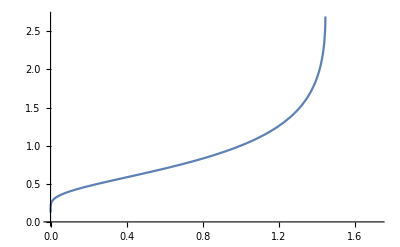

```mathematica
Plot[Tetrate[x,Infinity],{x,0,E-1}]
```

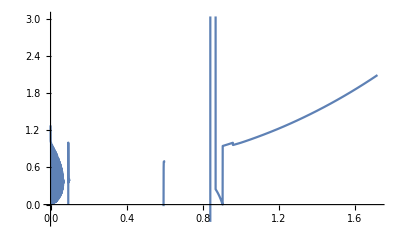

```mathematica
Plot[HalfExp[x],{x,0,E-1}]
```

```mathematica
env=Tetration`Private`Log4Prepare[10,x];
```

```mathematica
Tetration`Private`TetrationEvaluate[env,Tetration`Private`Log4Evaluate[env,x]+1/2]
```

Tetration`Private`TetrationEvaluate[{x,{1}},1/2+Tetration`Private`Log4Evaluate[{x,{-1. (1/1-1),8,1/1}},x]]
 |  |  |  |

```mathematica
Subfactorial[x]//FunctionExpand
```

Gamma[1+x,-1]/ⅇ

```mathematica
Factorial2[n]
```

n!!

```mathematica
InternalSeries
```

TetraDFormat[…]

TetraDFormat[…]

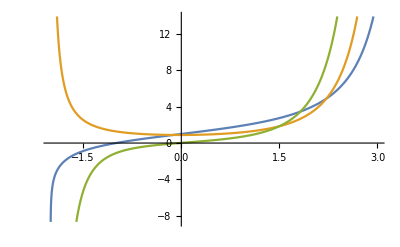

```mathematica
td=TetraD[Tetrate[2,x],x]
td2=TetraD[Tetrate[2,x],{x,2}]
Plot[{Tetrate[2,x],td[x],td2[x]},{x,-2,3}]
```

TetraDFormat[…]

TetraDFormat[…]

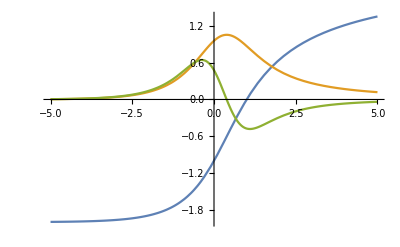

```mathematica
td=TetraD[TetraLog[3,x],x]
td2=TetraD[TetraLog[3,x],{x,2}]
Plot[{TetraLog[3,x],td[x],td2[x]},{x,-5,5}]
```

TetraDFormat[…]

TetraDFormat[…]

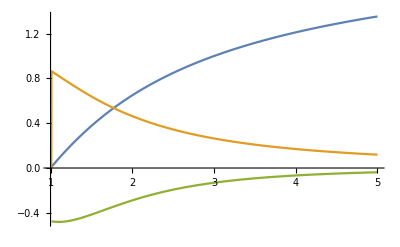

```mathematica
td=TetraD[TetraRoot[3,x],x]
td2=TetraD[TetraRoot[3,x],{x,2}]
Plot[{TetraRoot[3,x],td[x],td2[x]},{x,1,5}]
```

```mathematica
(*
**Usage:
**env=SuperLogPrepare[n,x];**SuperLog[env,z]-- gives n-th approx.of slog_x(z)**Tetrate[env,y]-- gives n-th approx.of x^^y**Copyright 2005 Andrew Robbins*)SuperLogPrepare[n_Integer,x_]:={x,LinearSolve[Table[k^j/k!-If[j==k,Log[x]^-k,0],{j,0,n-1},{k,1,n}],Table[If[k==1,1,0],{k,1,n}]]}
SuperLog[v_,z_?NumericQ]:=Block[{(*SlogCrit*)},SlogCrit[zc_]:=-1+Sum[v[[2,k]]*zc^k/k!,{k,1,Length[v[[2]]]}];
Which[z≤0,SlogCrit[v[[1]]^z]-1,0<z≤1,SlogCrit[z],z>1,Block[{i=-1},SlogCrit[NestWhile[Log[v[[1]],#]&,z,(i++;#>1)&]]+i]]]
(*Gives the k-th numerical derivative of f(x) at x=c:*)
ND[f_,x_,c_]:=ND[f,x,c,1]
ND[f_,x_,c_,k_]:=ND[f,x,c,k,0.0001]
ND[f_,x_,c_,0,h_]:=(f/.x->c)
ND[f_,x_,c_,k_,h_]/;k≠0:=(ND[f,x,c+h,k-1,h]-ND[f,x,c,k-1,h])/h
25
(***************************************)
(*A few commands to try for starters:*)
(***************************************)
(*Prepares the 10th approx.of slog_e(z):*)
(*the'=' is used here for immediate execution*)
(*the';' is used here to suppress display*)
```

25

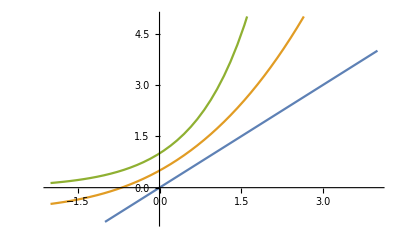

```mathematica
env=SuperLogPrepare[10,E];
(*Shows e^^0.5,and plots of e^^y:*)
(*f(x) such that f(f(x))=exp(x)*)
HalfExp2[x_]:=Tetration`Private`TetrationEvaluate[env,TetraLog[E,x]+1/2]
Plot[{x,HalfExp2[x],HalfExp2[HalfExp2[x]]},{x,-2,4},PlotRange->{-1,5}]
```